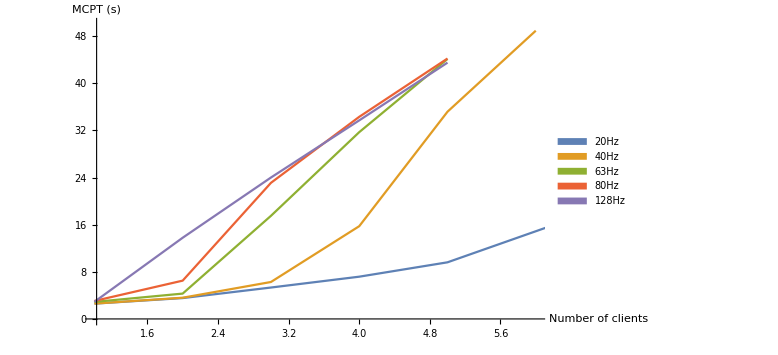

```mathematica
meanchunkprocessingtime128 = {{1,2.9},{2,13.78},{3,24}, {4,33.7},{5,43.5}};
meanchunkprocessingtime80 = {{1,3.05},{2,6.5},{3,23.1},{4,34.3},{5,44.2}};
meanchunkprocessingtime63 = {{1,2.89},{2,4.3},{3,17.5},{4, 31.7},{5,44.12}};
meanchunkprocessingtime20 = {{1,2.6},{2,3.54},{3,5.33},{4, 7.17},{5,9.61},{7,20.15}};
meanchunkprocessingtime40 = {{1,2.6},{2,3.6},{3,6.27},{4, 15.74},{5,35.17}, {6,48.92}};

ListPlot[{meanchunkprocessingtime20,meanchunkprocessingtime40,meanchunkprocessingtime63,meanchunkprocessingtime80, meanchunkprocessingtime128}, Joined->True, AxesLabel->{"Number of clients", "MCPT (s)"},PlotLegends->SwatchLegend[{"20Hz","40Hz", "63Hz","80Hz", "128Hz"}],PlotRange->{{1,6}, {0,50}}, ImageSize->Large]
```